# Isosceles Right Triangle

### Author

Eric W. Weisstein
July 31, 2026

This notebook downloaded from https://mathworld.wolfram.com/notebooks/Triangles/IsoscelesRightTriangle.nb.

For more information, see Eric's MathWorld entry https://mathworld.wolfram.com/IsoscelesRightTriangle.html.

©2026 Wolfram Research, Inc. except for portions noted otherwise

## Definitions

```mathematica
ineq=y≥0&&a≥x+y&&x≥0;
```

```mathematica
implreg=ImplicitRegion[ineq,{x,y}];
```

```mathematica
reg=Triangle[{{0,0},{0,a},{a,0}}];
```

```mathematica
assum=a>0;
```

```mathematica
t=reg;
```

## Figure

### PlaneGeometry.m

```mathematica
r=right/.{a->1};
v=Vertices[r];
pts={v[[1]],C,v[[2]],A,v[[3]],B};

Show[Graphics[{r,
{VertexArc[#,.17],EqualAngleTicks[#,1,.17,.05,0]}&/@NestList[RotateRight,RotateLeft[v],1],
PerpSquare[Rest[Sides[r]],.1,4],
PointLabels[r,pts,.03,-.05]
},AspectRatio->Automatic]
]
```

⁃Graphics⁃

### Height

```mathematica
SSSTriangle[1,1,√2]
```

Triangle[{{0,0},{√2,0},{1/(√2),1/(√2)}}]

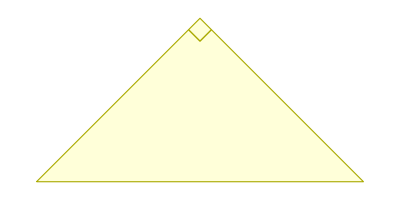

```mathematica
With[{s=.07},Graphics[{
FaceForm[LightYellow],EdgeForm[Darker@Yellow],SSSTriangle[1,1,√2],
{Darker@Yellow,Line[{1/(√2),1/(√2)}+RotationMatrix[-3π/4].#&/@{{s,0},{s,s},{0,s}}]}
}]]
```

## Equations

### Inequality

Rehashing named triangle objects...

```mathematica
right=Triangle[{{0,0},{a,0},{0,a}}];
```

```mathematica
FullSimplify[Inequalities[right,{x,y}],a>0]
```

y≥0&&a≥x+y&&x≥0

```mathematica
ineq[x_,y_]:=y≥0&&a≥x+y&&x≥0
```

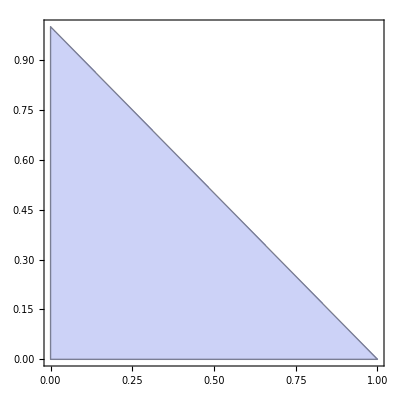

```mathematica
RegionPlot[ineq[x,y]/.a->1,{x,0,1},{y,0,1}]
```

## Plots

### Diagram

```mathematica
Show[LaminaData["FilledIsoscelesRightTriangle","Diagram"],Axes->False]
```

-Graphics-

### DiscretizeRegion

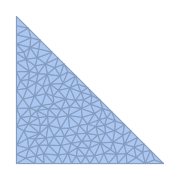

```mathematica
Block[{a=1},Show[DiscretizeRegion[reg],ImageSize->Small]]
```

### RegionPlot

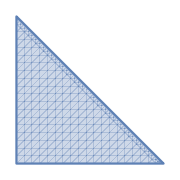

```mathematica
Block[{a=1},RegionPlot[ineq,{x,0,a},{y,0,a},AspectRatio->Automatic,ImageSize->Small,Frame->False]]
```

## Properties

### Area

#### Area

```mathematica
Assuming[assum,Simplify@Area[reg]]
```

a^2/2

#### Integrate

```mathematica
Assuming[a>0,Area[ineq[x,y],{x,y}]]//FullSimplify//Timing
```

{0.318801,a^2/2}

#### RegionMeasure

```mathematica
Assuming[assum,Simplify@RegionMeasure[reg]]
```

a^2/2

#### TriangleArea

```mathematica
TriangleArea[right]
```

a^2/2

### Centroid

#### Integrate

```mathematica
Assuming[a>0,Centroid[ineq[x,y],{x,y}]]//FullSimplify//Timing
```

{1.43544,{a/3,a/3}}

#### RegionCentroid

```mathematica
Assuming[assum,Simplify@RegionCentroid[reg]]
```

{a/3,a/3}

### Circumcircle

```mathematica
FullSimplify[Circumcircle[t],𝒶>0]/.𝒶->a
```

Circle[{a/2,a/2},a/(√2)]

### Circumradius

```mathematica
FullSimplify[PowerExpand[Circumradius[right]]]
```

a/(√2)

```mathematica
r=right/.a->1;
v=Vertices[r];
c=Circumcenter[r];
bluepts={c,O};

Show[Graphics[{
r,
PerpSquare[Rest[Sides[r]],.05,4],
{VertexArc[#,.1],EqualAngleTicks[#,1,.1,.04,0]}&/@NestList[RotateRight,RotateLeft[v],1],
{
Blue,
PointLabels[r,bluepts,.03,.05],
Circumcircle[r],
Line[{Coordinates@c,Vertices[r][[1]]}]
},
PointLabels[r,pts,.03,-.05]
},AspectRatio->Automatic]
]
```

⁃Graphics⁃

### SideLengths

```mathematica
abc=Simplify[SideLengths[Evaluate[t]],𝒶>0]
```

{√2 𝒶,𝒶,𝒶}

### Hypotenuse

```mathematica
PowerExpand[SideLengths[right]]
```

{√2 a,a,a}

### Incircle

```mathematica
FullSimplify[Incircle[t],𝒶>0]/.𝒶->a
```

Circle[{a-a/(√2),a-a/(√2)},a-a/(√2)]

### Inradius

```mathematica
r=right/.{a->1};
i=Incenter[r];
v=Vertices[r];

pts={v[[1]],C,v[[2]],A,v[[3]],B};
bluepts={i,"
StyleBox[\"I\",\nFontSlant->\"Italic\"]"};
Show[Graphics[{
r,
PerpSquare[Rest[Sides[r]],.05,4],
{VertexArc[#,.1],EqualAngleTicksAboutBisectors[#,1,.1,.03,0]}&/@NestList[RotateRight,RotateLeft[v],1],
{Thickness[.01],Incircle[r]},
{
Red,
PerpSquare[#,.05,2]&/@Transpose[{PedalLines[r,i],Sides[r]}],Dashing[{.02,.02}],
PedalLines[r,i]
},
{
Blue,
PointLabels[r,bluepts,.03,.05],Line[{#[[1]],Coordinates@i,#[[2]]}]&/@Partition[Vertices[r],2,1,1]
},
PointLabels[r,pts,.03,-.05]
},AspectRatio->Automatic]
]
```

⁃Graphics⁃

```mathematica
i=FullSimplify[PowerExpand[Inradius[right]]]
```

a-a/(√2)

```mathematica
Collect[%,a]
```

(1-1/(√2)) a

```mathematica
Together[%]
```

-1/2 (-2+√2) a

### InertiaTensor

```mathematica
Assuming[a>0,AreaInertiaTensor[ineq[x,y],{x,y}]]//FullSimplify//Timing
```

{1.5012,{{a^4/12,-a^4/24},{-a^4/24,a^4/12}}}

### RadiiOfGyration

```mathematica
Assuming[a>0,FullSimplify[RadiiOfGyration[ineq[x,y],{x,y}]]]//Timing
```

{1.01361,{a/(√6),a/(√6)}}

### GeneralizedDiameter

```mathematica
ineqs=FullSimplify[And@@ineq@@@{{x1,y1},{x2,y2}},a>0]/.a->1
```

y1≥0&&1≥x1+y1&&x1≥0&&y2≥0&&1≥x2+y2&&x2≥0

```mathematica
Maximize[{(x1-x2)^2+(y1-y2)^2,ineqs},{x1,x2,y1,y2},Reals]//Timing
```

{1.8923,{2,{x1→0,x2→1,y1→1,y2→0}}}